```mathematica
α=1;β=1;γ=1;δ=1;
```

```mathematica
p1eq=D[u[t],{t,2}]==6 u[t]^2+t
```

u''[t]==t+6 u[t]^2

```mathematica
p1sln=u[t]/.First@NDSolve[{p1eq,u[0]==0,u'[0]==0},u[t],{t,0,1}]
```

InterpolatingFunction[…][t]

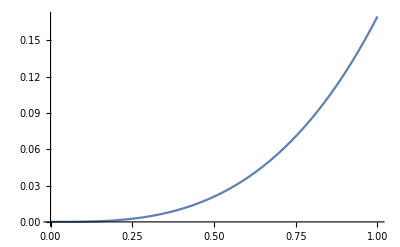

```mathematica
Plot[p1sln,{t,0,1}]
```

```mathematica
p2eq=D[u[t],{t,2}]==2 u[t]^3+t u[t]+α
```

u''[t]==1+t u[t]+2 u[t]^3

```mathematica
p2sln=u[t]/.First@NDSolve[{p2eq,u[0]==0,u'[0]==0},u[t],{t,0,1}]
```

InterpolatingFunction[…][t]

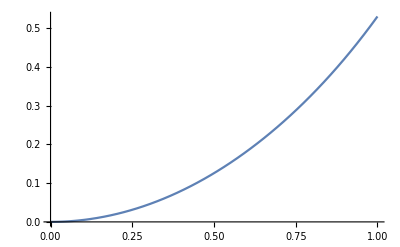

```mathematica
Plot[p2sln,{t,0,1}]
```

```mathematica
p3eq=t u[t]*D[u[t],{t,2}]==t D[u[t],t]^2-u[t] D[u[t],t]+δ t+β u[t]+α u[t]^3+γ t u[t]^4
```

t u[t] u''[t]==t+u[t]+u[t]^3+t u[t]^4-u[t] u'[t]+t u'[t]^2

```mathematica
p3sln=u[t]/.First@NDSolve[{p3eq,u[1]==1,u'[1]==0},u[t],{t,1/4,9/4}]
```

NDSolve::ndsz: At t == 2.13599, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…][t]

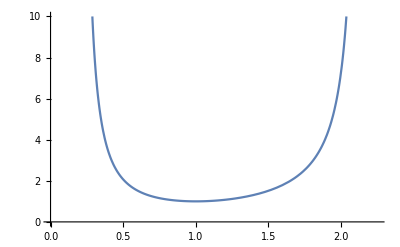

```mathematica
Plot[p3sln,{t,1/4,9/4},PlotRange->{0,10}]
```